# Network Dynamics & Centrality Analysis

This project investigates how the structure of a network affects the dynamical importance of its nodes and links. Using adjacency-matrix representations, stochastic network generation, eigenvalue analysis and iterative simulation, the analysis compares several network structures and examines how they respond to changes in individual nodes and links. The project draws on the framework developed by Restrepo, Ott and Hunt (2006).

Originally developed as part of the ECON0114 module during my Economics BSc at University College London (2020/21).

### Random Network Generation & Analysis

This section investigates how the structural properties of different random networks affect the dynamical importance of their nodes and links. I first construct Erdős–Rényi and spatial network models, then compare their statistical properties across repeated simulations. I subsequently calculate node and link dynamical importance, compare the results with theoretical approximations, and examine how these relationships change under different network parameters.

## Network Models

Two random network models are considered. The first is an Erdős–Rényi network in which links are generated independently with a fixed probability. The second is a spatial network in which nodes are assigned positions in two-dimensional space and the probability of a connection depends on the distance between them.

The following command generates an adjacency matrix for an Erdos-Rényi network consisting of 100 nodes with no self-loops in which the probability of any link i→j existing, where i≠j, is given by p:

```mathematica
Subscript[A, 1][p_,n_]:=Table[If[i==j,0,If[RandomReal[]<p,1,0]],{i,1,n},{j,1,n}]
```

Meanwhile, the following command generates a list of n points in a two-dimensional space named Nodes, where the x coordinate of each point is initially drawn from a uniform distribution on the interval [0,10] and the y coordinate is then drawn from a normal distribution such that the expected value of y for a point with x coordinate given by x^* is given by 10-x^*, while the standard deviation for the y coordinate is given by α/(β^(|5-x^*|)), where α and  β require specification:

```mathematica
Y[α_,β_,n_]:=Do[{x={RandomReal[{0,10}]},y=RandomVariate[NormalDistribution[10-x[[1]],α 1/β^Abs[5-x[[1]]]]],z=AppendTo[x,y],AppendTo[Nodes,z]},n]
```

Note that for large β, as the value of the x coordinate deviates away from the 5, the standard deviation of the normal distribution from which the y coordinate is drawn approaches zero and its value converges to 1-x, which ensures that for extreme values of x, the value of y remains on the interval [0,10] for sufficiently large β. Note also that the larger is the value of β, the more rapidly the value of y converges to 1-x as we deviate from x=5. Meanwhile, note that for x very close to 5, the standard deviation of the distribution for y is given by approximately α which is independent of the value of β. Thus, the larger the value of α, the greater is the variance of y for points with x close to 5, which will result in the average distance between such points increasing. Now, the command GD below allows us to compute the geometric distance between any two points that belong to Nodes, while the command SW simply takes GD to the power γ, where γ requires specification:

```mathematica
GD[Label1_,Label2_]:=√((Label1[[1]]-Label2[[1]])^2)+√((Label1[[2]]-Label2[[2]])^2);SW[Label1_,Label2_,γ_]:= GD[Label1,Label2]^γ
```

The command below generates an adjacency matrix for a network with no self-loops where the probability that the link i→j exists for i≠j is given by p/Max[1,D[i,j]^γ], with D[i,j] being the geometric distance between the points representing the nodes i and j:

```mathematica
Subscript[A, 2][p_,γ_]:=Table[If[i==j,0,RandomChoice[{p/Max[SW[Nodes[[i]],Nodes[[j]],γ],1],1-p/Max[SW[Nodes[[i]],Nodes[[j]],γ],1]}->{1,0}]],{i,1,Length[Nodes]},{j,1,Length[Nodes]}]
```

Note that the probability that the link i→j exists is equal to the probability that the link j→i exists, so that the adjacency matrix corresponding to such a network is symmetric in expectation.

## Repeated Network Simulations

To compare the statistical properties of the two network models, I generate repeated samples of networks using fixed parameter values. Node positions are regenerated for each spatial network so that the results capture variation in both network connections and the underlying spatial distribution of nodes.

The command below generates a sample of M adjacency matrices corresponding to Erdos-Rényi networks with no self-loops and consisting of n agents, where each link  i→j satisfying i≠j has probability p of existing:

```mathematica
Sample[p_,n_,M_]:=Table[Subscript[A, 1][p,n],{i,1,M}]
```

We now generate a sample of 10000 such networks satisfying p=0.1 and n=100:

```mathematica
SampleA=Sample[0.1,100,10000];
```

The Do command below generates a list of points in a two-dimensional space with coordinates drawn from the distributions described previously, where the standard deviation of the normal distribution from which the y coordinates of the points are drawn has parameters α and β set to 4 and 5 respectively. In this case, the value of β is large enough to ensure that y converges to 1-x for x sufficiently close to 1 and 10, which makes almost certain that it remains on the interval [0,10] as we move away from x=5, but also small enough so that we get a sufficiently large number of points close to x=5 with y that deviates from y=1-x. Meanwhile, the value of α is large enough to induce a sufficiently large degree of variance in the value of y for points with x close to 5, while small enough to ensure that the majority of these points stay on the interval [0,10], with the y coordinates of roughly 95% of such points falling on the interval [5-2σ,5+2σ]=[-3,13] for the values of x in question. Note that for such a sprinkling of points in the plane, we would expect nodes corresponding to points with x coordinates close to 5 to have both a low in-degree and low out-degree for positive γ due to the low density of nodes in this region of the plane. Meanwhile, we would expect nodes corresponding to points with x coordinates close to 10 or close to 1 to have both a high in-degree and high out-degree for positive γ due to the high density of nodes in these regions of the plane. Furthermore, for this configuration we would expect nodes with a high degree to be connected to other nodes with a high degree and vice versa. As a result, for positive γ we would expect the function A_2[p,γ] to generate an adjacency matrix that corresponds to an assortative network, with the assortativity of the network increasing in γ. Conversely, by the same reasoning, for negative γ we would expect the function in question to generate an adjacency matrix that corresponds to a disassortative network, with the assortativity of the network decreasing in the absolute value of γ. Now, once the command below has generated the list of points corresponding to our chosen distributions, it produces an adjacency matrix for a network where the probability of a link between two nodes existing depends on the geometric distance between the points corresponding to the nodes in question in the desired manner, and appends this adjacency matrix to a list. The command repeats this process 10000 times to produce a sample of 10000 networks, each of which corresponds to a different scattering of points with coordinates drawn from the distributions specified above. The reason that we don’t generate a sample of networks according to one draw of 100 points in the plane is due to the possibility that such a scattering is an outlier and thus not representative of the class of networks in question. Thus, we have two sources of randomness entering into the sample generated below:

```mathematica
SampleB={};Do[{Nodes={},Y[4,5,100],AppendTo[SampleB,Subscript[A, 2][0.1,0.75]]},10000]
```

We now introduce the matrix Q, which has the property that all of its elements, with the exception of those on its diagonal, take a value of 1. Then, for an unweighted adjacency matrix A, element (k,k) of the matrix A.Q.A yields the number of two step paths through node k of the network corresponding to the adjacency matrix A excluding two step closed paths as required for the computation of the Newman clustering coefficient:

```mathematica
Q[n_]:=Table[1,{j,1,n},{i,1,n}]-IdentityMatrix[n]
```

The function below now computes the Newman clustering coefficient, which is defined as the ratio of the total number of triangles (where we count triangles which are undirected twice) to the total number of two step paths for a network corresponding to the adjacency matrix A:

```mathematica
NewmanClustering[A_]:=(1/3 Tr[MatrixPower[A,3]])/Tr[A.Q[Length[A]].A]
```

The following commands calculate the Newman clustering coefficient for every network in SampleA and SampleB respectively:

```mathematica
NC1=Map[NewmanClustering,SampleA];NC2=Map[NewmanClustering,SampleB];
```

Below are the distributions for the Newman clustering coefficient across SampleA (leftmost figure) and SampleB (rightmost figure):

```mathematica
GraphicsGrid[{{Histogram[NC1,"Probability",Frame->True,FrameLabel->{"NC","P(NC)"}],Histogram[NC2,"Probability",Frame->True,FrameLabel->{"NC","P(NC)"}]}}]
```

Figure 1:

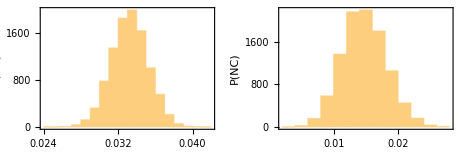

Thus, we see that in general the networks in SampleA have a greater Newman clustering coefficient than the networks in SampleB. Note that the links in a SampleB network are expected to be a subset of the links that exist in a SampleA network, since the probability that a given link exists in SampleA is at least as large as the probability that the corresponding link exists in SampleB, so the fact that nodes in this network exhibit a lower propensity to cluster is no surprise. Now, the following command computes the numerical value of the largest eigenvalue in absolute value of a matrix A:

```mathematica
EvA[A_]:=Eigenvalues[N[A]][[1]]
```

The following commands calculate the largest eigenvalue for every network in SampleA and SampleB respectively:

```mathematica
Ev1=Re[Map[EvA,SampleA]];Ev2=Re[Map[EvA,SampleB]];
```

Below are the distributions for the largest eigenvalue across SampleA (leftmost figure) and SampleB (rightmost figure):

```mathematica
GraphicsGrid[{{Histogram[Ev1,"Probability",Frame->True,FrameLabel->{"λ","P(λ)"}],Histogram[Ev2,"Probability",Frame->True,FrameLabel->{"λ","P(λ)"}]}}]
```

Figure 2:

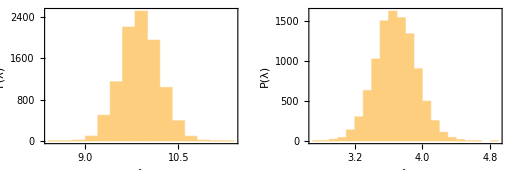

Note that the largest eigenvalues of the adjacency matrices in SampleA most frequently take a value close to 10, which is in line with what we would anticipate. Note that an Erdos-Rényi network with n agents that has no self-loops and has probability p of any given link existing has the property that it is expected to have largest eigenvalue in absolute value given by (n-1)p, which in our case yields 9.9. Thus, the leftmost figure above is in line with our expectation. Meanwhile, the largest eigenvalues of the adjacency matrices in SampleB tend to be smaller than those in SampleA. This is a result of the fact that the links in a SampleB network are expected to be a subset of the links that exist in a SampleA network, since the probability that a given link exists in SampleA is at least as large as the probability that the corresponding link exists in SampleB, and removing a link from a network will always have the effect of reducing the largest eigenvalue of the corresponding adjacency matrix, as we will see. Finally, note the greater variability in the value of the largest eigenvalue for adjacency matrices in SampleB. This most likely results from the fact that we chose to generate a new scattering of points for each subsequent network generated in the sample. Now, in order to derive the assortativity for each network in our samples, we must define three functions, the first being the mean number of three-step paths through a link:

```mathematica
Subscript[E, T][A_]:=(Total[A].A.Total[Transpose[A]])/Total[Total[A]]
```

We also require the average of the in-degrees and out-degrees of two nodes connected by a link:

```mathematica
Subscript[E, S][A_]:=(Total[A].Total[Transpose[A]])/Total[Total[A]]
```

Finally, we require the variance in the mean number of in-links and out-links at a link i→j:

```mathematica
Subscript[Var, S][A_]:=(1/4(∑_(i=1)^Length[A] (Total[A][[i]])^3+∑_(i=1)^Length[A] (Total[Transpose[A]][[i]])^3))/Total[Total[A]]+1/2 Subscript[E, T][A]-(Subscript[E, S][A])^2
```

Then, the assortativity for a network corresponding to the adjacency matrix A is given by the function below:

```mathematica
Assortativity[A_]:=(Subscript[E, T][A]-(Subscript[E, S][A])^2)/(Subscript[Var, S][A])
```

The following commands calculate the coefficient of assortativity for every network in SampleA and SampleB respectively:

```mathematica
AS1=Map[Assortativity,SampleA];AS2=Map[Assortativity,SampleB];
```

Below are the distributions for the assortativity across SampleA (leftmost figure) and SampleB (rightmost figure):

```mathematica
GraphicsGrid[{{Histogram[AS1,"Probability",Frame->True,FrameLabel->{"A","P(A)"}],Histogram[AS2,,"Probability",Frame->True,FrameLabel->{"A","P(A)"}]}}]
```

Figure 3:

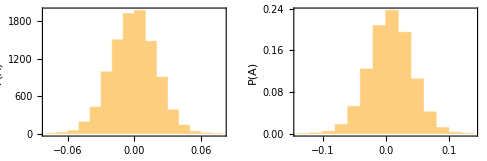

Note that the plot above shows us that the Erdos-Rényi networks in SampleA are expected to have an assortativity of zero. This is anticipated, since for such networks links are placed at random without regard to node degree, from which it follows that, for sufficiently large networks, we would expect an assortativity of zero for this class of networks. Meanwhile, as anticipated, the networks in SampleB are expected to have a small and positive reading as a result of the fact that we have set both p and γ equal to small positive values.

## Link Dynamical Importance

I calculate the dynamical importance of each possible link by modifying the corresponding entry in the adjacency matrix and measuring the resulting relative change in the network’s largest eigenvalue.

The command below takes the component (i,j) of an adjacency matrix A and generates a new matrix with the same dimensions that has all entries equal to zero other than the entry (i,j), which takes a value of 1 if the component (i,j) of the original matrix takes value 0 and -1 if the component (i,j) of the original matrix takes a value of 1.

```mathematica
R[A_,i_,j_]:=If[A[[i,j]]==1,Table[If[k==i && l==j,-1,0],{k,1,Length[A]},{l,1,Length[A]}],Table[If[k==i && l==j,1,0],{k,1,Length[A]},{l,1,Length[A]}]]
```

Now, the Do command below takes a component of an adjacency matrix A and replaces it with 0 if the original entry was 1 (which represents the removal of a link if it exists) and with 1 if the original entry was 0 (which represents the addition of a link if it doesn’t exist) by adding the output of the command R for the component in question to the original adjacency matrix. The command then calculates the relative change in the largest eigenvalue with respect to the original adjacency matrix for this new adjacency matrix (called B), and appends the result to the list ΔEvl. It does this for all components of the original adjacency matrix A. Note that element k of the list ΔEvl corresponds to the relative change in the value of the largest eigenvalue when we add/remove the link Ceiling[k/100]→If[k/100∈Integers,100,k-100 Floor[k/100]] from the network represented by the original adjacency matrix A. Note that in order to maximise the speed of the calculation described, we have written the function d below so that the largest eigenvalue of the original matrix A is specified as an input, which prevents the Do command from having to recalculate the eigenvalue in question for each of its iterations.

```mathematica
d[A_,λ_]:=Do[{B=A+R[A,i,j],μ=Eigenvalues[B][[1]],AppendTo[ΔEvl,(μ-λ)/λ]},{i,1,Length[A]},{j,1,Length[A]}]
```

## Theoretical Approximation

For an example of each network type, I compare the exact link dynamical importance with the eigenvector-based theoretical approximation proposed by Restrepo, Ott and Hunt.

Note that for a matrix A that satisfies the conditions of the Perron-Frobenius theorem, we know that the largest eigenvalue λ of A is positive and real. Furthermore, using the spectral representation of A, we can show that A^m.𝕀⃗≈λ^m(u⊗v).𝕀⃗=λ^m(v.𝕀⃗)u and that 𝕀⃗.A^m≈λ^m 𝕀⃗.(u⊗v)=λ^m(u.𝕀⃗)v, where u and v are the right and left eigenvectors respectively corresponding to the eigenvalue of A with largest absolute value. Note that entry k of the vector A^m.𝕀⃗ yields the number of m-step outgoing links from node k while entry k of the vector 𝕀⃗.A^m yields the number of m step links into node k for the network corresponding to A. Thus, the change in the value of λ upon the removal of an existing link or node are a measure of the degree to which said removal affects the number of multiple step paths through all of the nodes in the network and is thus a global measure, which distinguishes it from the measure of eigenvector centrality. For example, we might have a network consisting of two subgraphs, with one subgraph very large and one very small. Now, it may be that a node in the smaller subnetwork has a very large eigenvector centrality relative to other nodes, but because this node is completely disconnected from the large subnetwork, its dynamical importance will be low. Note also that the reasoning above obviously implies that the removal of a node or link will always lead to a reduction in the largest eigenvalue of the corresponding adjacency matrix. Now, the command below generates an Erdos-Rényi network A1 consisting of 100 nodes with no self-loops where there is a probability 0.1 of any link i→j (such that i≠j) existing. It then generates a list ΔEvl1 containing, for each possible link in the network, the relative change in the largest eigenvalue of A1 when we add/remove a given link from the network. In order to increase the speed of computation, we amend the function d[A,λ] above so that it calculates the numerical change in the largest eigenvalue when we add/remove a link from the network:

```mathematica
A1=Subscript[A, 1][0.1,100];Subscript[λ, 1]=Eigenvalues[N[A1]][[1]];ΔEvl1={};d[A1,Subscript[λ, 1]]
```

The command below now generates a list of points in two-dimensional space with coordinates drawn from the distributions described in the first sub-question of part A:

```mathematica
Nodes={};Y[4,5,100]
```

The scattering of points that is generated by the command above is shown below:

```mathematica
ListPlot[Nodes,PlotRange->Full,Frame->True,FrameLabel->{"x","y"}]
```

Figure 4:

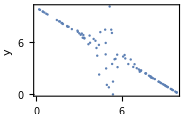

In the analysis that follows, we will generate all networks of the type A2 according to the distribution of points above. This will allow us, for example, to see which node has the highest dynamical importance in the network, and locate the point associated with that particular node. Now, the command below generates a network of the second type A2 with parameters p=0.1 and γ=0.75 and produces the corresponding list of dynamical importances of links ΔEvl2 for this network:

```mathematica
A2=Subscript[A, 2][0.1,0.75];Subscript[λ, 2]=Eigenvalues[A2][[1]];ΔEvl2={};d[A2,Subscript[λ, 2]]
```

The function below now allows us to apply equation (4) from the paper by Restrepo, Ott and Hunt (2006) to each entry of an adjacency matrix A:

```mathematica
b[A_,u_,v_,λ_]:=Flatten[Table[A[[i,j]]Re[(v[[i]]u[[j]])/(λ v.u)],{i,1,Length[A]},{j,1,Length[A]}]]
```

The command below calculates the left and right eigenvectors corresponding to the eigenvalue of largest absolute value for the adjacency matrices associated with the networks A1 and A2 respectively:

```mathematica
v1=Eigenvectors[Transpose[N[A1]]][[1]];u1=Eigenvectors[N[A1]][[1]];v2=Eigenvectors[Transpose[N[A2]]][[1]];u2=Eigenvectors[N[A2]][[1]];
```

The two plots below now show how accurately the dynamical importance of the nodes in each of the networks A1 and A2 are represented by equation (4) from the paper by Restrepo, Ott and Hunt (2006). The leftmost plot corresponds to the case of the network A1, which shows that there is a linear relationship between equation (4) and dynamical importance, and while the relative ranking of the nodes in terms of dynamical importance is mostly preserved by the approximation, there are deviations which result from the fact that second order terms are neglected. Specifically, it is assumed in the paper that the changes in the components of the right eigenvector u corresponding to the largest eigenvalue λ as well as λ itself are small when we remove a link. However, for a network that has a small number of links this will not be the case. To see this more clearly, consider a network that is highly connected. For such a network, we would have a large number of multiple step paths running through each node. Now, by removing a link from the network, the eigenvector components corresponding to the nodes that had a large number of multiple step paths which included the removed link running through them prior to the link’s removal will incur a disproportionate reduction, while the magnitude of the reduction in the largest eigenvalue will depend on how central the link was to far reaching connections within the network. In the case of a highly connected network however, these reductions will be small, since the removal of the link will only reduce the number of multiple step paths in the network by a small percentage relative to the number of these paths that existed in the first place. This means that the largest eigenvalue and the components of the corresponding right eigenvector will only change by a small amount relative to their initial values for such networks. However, for the network A1 which was generated by setting p equal to 0.1, the number of links in the network is relatively small, meaning that Δu and Δλ will be large when links with high dynamical importance are removed, resulting in equation (4) failing to maintain the ordering of the links with respect to dynamical importance in this case.

```mathematica
GraphicsGrid[{{ListPlot[Table[{If[A1[[Ceiling[i/100],If[i/100∈Integers,100,i-100 Floor[i/100]]]]>0,b[A1,u1,v1,Subscript[λ, 1]][[i]],Indeterminate],-ΔEvl1[[i]]},{i,1,10000}],Frame->True,FrameLabel->{"(Î)_ij","I_ij"}],ListPlot[Table[{If[A2[[Ceiling[i/100],If[i/100∈Integers,100,i-100 Floor[i/100]]]]>0,b[A2,u2,v2,Subscript[λ, 2]][[i]],Indeterminate],-ΔEvl2[[i]]},{i,1,10000}],Frame->True,FrameLabel->{"(Î)_ij","I_ij"}]}}]
```

Figure 5:

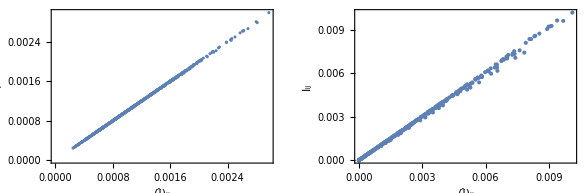

Meanwhile, the rightmost plot above corresponds to the case of the network A2. The links in this network are expected to be a subset of the links that exist in the network A1 as we have mentioned. Due to the fact that A2 will have less links in expectation than A1, we would expect equation (4) to maintain the ordering of links in terms of their dynamical importance to an even lesser degree when applied to A2. To compound this, network A2 is also assortative, which means that links connected to nodes with a high out-degree on one end (which are also expected to have a high in-degree due to the symmetry of the probabilities of a link existing in the network A2) will be expected to connect to links with high in-degree on the other. The removal of such links will result in large changes to the components of u and λ, which results in equation (4) becoming even more obsolete in this case. Note finally that the assortativity of the second type of network being studied is not only increasing in γ, but also in p (assuming that γ is positive; for negative γ, increasing the value of p will lead to a reduction in the assortativity of the network being generated), since randomness is eliminated and the distances between points corresponding to nodes become the sole factors which determine the probability of certain links existing for large p. For such networks with large p and γ, on the one hand we would expect equation (4) to maintain the ordering of links in terms of their dynamical importance to a greater extent due to the greater connectedness of the network, but on the other hand we might expect a high assortativity reading to counter this effect. We will study this with respect to the nodes of the class of networks of interest rather than their links in the sixth sub-question of part A below.

## Node Dynamical Importance

I extend the analysis from links to nodes. Each node is disconnected by setting its corresponding row and column in the adjacency matrix to zero, and its dynamical importance is calculated from the resulting relative change in the largest eigenvalue. I then compare the exact values with the theoretical approximation.

The Do command below takes row and column k of a specified adjacency matrix A and sets all of their components to 0 (which represents the removal of all incoming and outgoing links corresponding to node k of the network described by A). The command then calculates the relative change in the largest eigenvalue with respect to the original adjacency matrix for this new adjacency matrix B, and appends the result to the list ΔEvn. It does this for all rows and columns of the original adjacency matrix A. Note that element l of the list ΔEvn corresponds to the relative change in the value of the largest eigenvalue when we add/remove the node l from the network represented by the original adjacency matrix A. Again, in order to maximise the speed of the calculation described, we have written the function f below so that value of the largest eigenvalue of the original matrix A is specified as an initial input.

```mathematica
f[A_,λ_]:=Do[{B=Transpose[ReplacePart[Transpose[ReplacePart[A,k->Table[0,Length[A]]]],k->Table[0,Length[A]]]],μ=Eigenvalues[B][[1]],AppendTo[ΔEvn3,(μ-λ)/λ]},{k,1,200}]
```

Now, in the paper by Restrepo, Ott and Hunt (2006), the authors generate a network where each node is assigned an expected in-degree d_k^in by using a function which is increasing in the magnitude of a node’s label k, while the expected out-degrees d_k^out of the nodes in question are assigned by randomly permuting the function output which assigns an expected in-degree to each node. This ensures that the in-degrees and out-degrees at each node are uncorrelated. The adjacency matrix for the network is then constructed by setting A_ij=1 for i≠j with probability proportional to d_i^out d_j^in. This generates a network with assortativity zero. The authors of the paper then modify the network in question by rearranging links in order to generate assortative and disassortative networks. Note that the Erdos-Rényi network A1 that we have generated is an example of the category of networks described above that has zero assortativity and zero correlation between the in-degree and out-degree of its nodes, with the difference being in our case that we have d_i^out=d_i^in=d_j^out=d_j^in for all i and j. Furthermore, by setting the parameter γ to a positive value for the network A2, we generate a network that has less links than A1 and with positive assortativity in expectation. Similarly, by setting γ to a negative value, we generate a network that has more links than the assortative network generated by setting γ>0, since there are more nodes with distance greater than 1 from any given node in the network than there are nodes with distance less than 1 from the node in question, and which is disassortative. Thus, in what follows, we generate networks of different coefficients of assortativity by varying γ and analyse the effect of this variable on the dynamical importances of the nodes which result as a function of degree, just as Restrepo, Ott and Hunt do. The command below now generates a list ΔEvn1 containing, for each possible node in the network, the relative change of the largest eigenvalue of A1 when we remove a given node. In order to increase the speed of computation, we amend the function f[A,λ] above so that it calculates only the numerical change in the largest eigenvalue when we remove a node:

```mathematica
ΔEvn1={};f[A1,Subscript[λ, 1]]
```

Similarly, the command below now generates the corresponding list of dynamical importances of nodes ΔEvn2 for this network:

```mathematica
ΔEvn2={};f[A2,Subscript[λ, 2]]
```

The two plots below now show how accurately the dynamical importance of the nodes in each of the networks A1 and A2 are represented by equation (5) from the paper by Restrepo, Ott and Hunt (2006). The leftmost plot corresponds to the case of the network A1, and while we see that there is a linear relationship between equation (5) and the dynamical importance, the relative ranking of the nodes in terms of dynamical importance is not preserved by the approximation. This is a result of the fact that for small values of p, percentage differences in total degree across nodes are larger than for networks with high values of p, which translates into large differences in eigenvector centrality across nodes. This means that the assumption v_k u_k<< v.u for all k is not satisfied, which reduces the accuracy of the approximation yielded by equation (5). To demonstrate this more clearly, suppose that we set p=0.9. In this case, the expected out-degree of a given node for a network of 100 agents with no self-loops is given by 89.1. Now, suppose that there is some variation in the out-degree across nodes, so that node i has an out-degree of 86 while node j has an out-degree of 94. In this case, the percentage difference in the out-degree across the two nodes is given by approximately 9%. As a result, due to the fact that the network is not assortative, we would not expect this difference in connectivity to be compounded across greater distances, so would therefore also expect the percentage difference in the right eigenvector centrality across the two nodes to be roughly 9%. On the other hand, if we set p=0.1, the expected out-degree of a given node is given by 9.9. Again, suppose that there is some similar variation in the out-degree across nodes, so that node i has an out-degree of 6 while node j has an out-degree of 14. In this case, the percentage difference in out-degree across the two nodes is given by roughly 13%, which we would expect to translate into a 13% difference in the right eigenvector centrality across the two nodes. Thus, in the second case, the potential for larger percentage differences in degree across nodes combined with the fact that Erdos-Rényi networks have zero assortativity in expectation means that the assumption that (v_k u_k)/(v.u)<<1 for all k is less likely to hold (especially given the relatively small size of the networks that we are analysing), meaning that equation (5) fails to maintain the ordering of the nodes in terms of their dynamical importance.

```mathematica
GraphicsGrid[{{ListPlot[Table[{-ΔEvn1[[k]],Re[(Eigenvectors[N[A1]][[1]][[k]]Eigenvectors[N[Transpose[A1]]][[1]][[k]])/(Eigenvectors[N[A1]][[1]].Eigenvectors[N[Transpose[A1]]][[1]])]},{k,1,100}],Frame->True,FrameLabel->{"I_k","(Î)_k"}],ListPlot[Table[{-ΔEvn2[[k]],Re[(Eigenvectors[N[A2]][[1]][[k]]Eigenvectors[N[Transpose[A2]]][[1]][[k]])/(Eigenvectors[N[A2]][[1]].Eigenvectors[N[Transpose[A2]]][[1]])]},{k,1,100}],Frame->True,FrameLabel->{"I_k","(Î)_k"}]}}]
```

Figure 6:

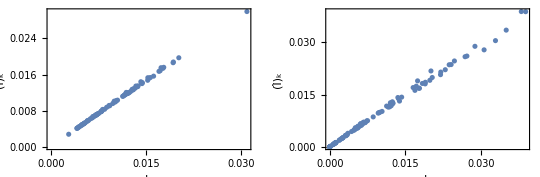

Meanwhile, the rightmost plot above corresponds to the case of the network A2. We see in this case that the ordering of the nodes is even less well preserved by equation (5). This is a result of the fact that network A2 has even less connections than A1, which compounds the effect described in the previous paragraph, but also reflects the fact that the network A2 is assortative, which accentuates differences in the total degree across nodes over longer distances and results in even greater differences in eigenvector centralities, resulting in the condition (v_k u_k)/(v.u)<<1 for all k failing. Thus, the deviation from linearity in the rightmost plot above is greater than in the leftmost plot as a result of the fact that the network A2 is assortative while A1 is not, and also due to the fact that A2 has a lower number of connections than does A1. The plots below now show the relationship between the dynamical importance of a node in the two networks generated and the root of the product of the in-degree and out-degree of the node in question (with the leftmost plot corresponding to the network A1). Note that since equation (5) does not preserve the ordering of the nodes in terms of their dynamical importance in either case, the vertical coordinates correspond to dynamical importances calculated from their definition:

```mathematica
GraphicsGrid[{{ListPlot[Table[{(Total[A1][[k]]Total[Transpose[A1]][[k]])^(1/2),-ΔEvn1[[k]]},{k,1,100}],PlotRange->Full,Frame->True,FrameLabel->{"(d_k^ind_k^out)^(1/2)","I_k"}],ListPlot[Table[{(Total[A2][[k]]Total[Transpose[A2]][[k]])^(1/2),-ΔEvn2[[k]]},{k,1,100}],PlotRange->Full,Frame->True,FrameLabel->{"(d_k^ind_k^out)^(1/2)","I_k"}]}}]
```

Figure 7:

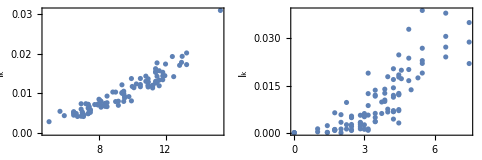

Note here that nodes in A2 with a low local connectedness also tend to have a low dynamical importance, but that the dynamical importance is very responsive to increases in the total degree of nodes. This is due to the fact that A2 is assortative, and so nodes with greater local connectedness will be connected to nodes that also have a high degree, resulting in a high dynamical importance reading. On the other hand, due to the fact that the network A1 is not assortative, the dynamical importance of a node is not as responsive to increases in its degree. We should also note the narrow range of values that (d_k^out d_k^in)^(1/2) takes in the leftmost plot above, which results from the fact that all nodes in the network are expected to have the same in-degree and out-degree.

## Parameter Sensitivity

I test whether the preceding results are representative by repeating the analysis across samples of randomly generated networks. I then vary network density and the spatial-network parameters to investigate how assortativity and network structure affect the relationship between node degree, dynamical importance and the accuracy of the theoretical approximation.

In what follows we restrict our analysis to the dynamical importances of nodes in the networks that we generate below, since the results that we derive will generalise very easily to the dynamical importance of links. The list SampleC below contains 500 adjacency matrices corresponding to networks of type A1 with the parameter p set to 0.1:

```mathematica
SampleC=SampleA[[1;;500]];
```

Meanwhile, the list SampleD below contains 500 adjacency matrices corresponding to networks of type A2 with the parameters p and γ set to 0.1 and 0.75 respectively:

```mathematica
SampleD={};Do[AppendTo[SampleD,Subscript[A, 2][0.1,0.75]],500]
```

The command below generates a matrix M1, where entry (i,j) of the matrix in question yields the dynamical importance of node j of the network corresponding to the adjacency matrix i in SampleC:

```mathematica
ΔEvnC={};Do[{λ=Eigenvalues[N[SampleC[[i]]]][[1]],f[SampleC[[i]],λ]},{i,1,Length[SampleC]}];M1=ArrayReshape[Re[ΔEvnC],{500,100}];
```

The command below now generates a plot which shows the relationship between the dynamical importance of a node and (d_k^in d_k^out)^(1/2) for networks in SampleC:

```mathematica
List1={};Do[{T=Table[{(Total[SampleC[[i]]][[k]]Total[Transpose[SampleC[[i]]]][[k]])^(1/2),-M1[[i,k]]},{k,1,100}],AppendTo[List1,T]},{i,1,Length[SampleC]}];L1=ListPlot[List1,PlotRange->Full,PlotStyle->Blue,Frame->True,FrameLabel->{"(d_k^ind_k^out)^(1/2)","I_k"}];
```

Once again, the command below generates a matrix M2, where entry (i,j) of the matrix in question yields the dynamical importance of node j of the network corresponding to the adjacency matrix i in SampleD:

```mathematica
ΔEvnD={};Do[{λ=Eigenvalues[N[SampleD[[i]]]][[1]],f[SampleD[[i]],λ]},{i,1,Length[SampleD]}];M2=ArrayReshape[Re[ΔEvnD],{500,100}];
```

Finally, the command below generates a plot which shows the relationship between the dynamical importance of a node in the two networks generated and (d_k^in d_k^out)^(1/2) for networks in SampleD:

```mathematica
List2={};Do[{T=Table[{(Total[SampleD[[i]]][[k]]Total[Transpose[SampleD[[i]]]][[k]])^(1/2),-M2[[i,k]]},{k,1,100}],AppendTo[List2,T]},{i,1,Length[SampleD]}];L2=ListPlot[List2,PlotRange->Full,PlotStyle->Red,Frame->True,FrameLabel->{"(d_k^ind_k^out)^(1/2)","I_k"}];
```

The figure below now shows the two plots generated above in the same plane, with the red plot corresponding to networks contained in SampleD and the blue plot corresponding to networks contained in SampleC:

```mathematica
Show[L1,L2]
```

Figure 8:

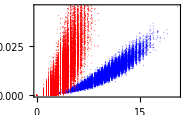

Note first of all that the points comprising the plot corresponding to the networks in SampleD above generally take smaller values on the horizontal axis, which is a result of the fact that the probability of any given link existing for the networks in this sample is smaller than the corresponding probability for the Erdos-Rényi networks in SampleC, which results in the average degree of nodes corresponding to networks in SampleD being significantly lower than in SampleC. Furthermore, we see that the rate of increase in the general trend of the red points is far greater than the corresponding rate of increase for the blue points, which is a result of the fact that the networks in SampleD are assortative, so that nodes with a high degree are likely to be connected to nodes which also have a high degree, leading to the dynamical importance of a node increasing significantly as it becomes more connected locally. Meanwhile, the Erdos-Rényi networks in SampleC will generally have an assortativity of zero, which means that the correlation between the degree of a node and its dynamical importance will be relatively low for reasons which we explained in the previous sub-question. Thus, the data above validates our initial findings for the networks A1 and A2 with parameter values p=0.1 and γ=0.75. Now, the list SampleE below contains 500 adjacency matrices corresponding to networks of the type A1 with the parameter p set to 0.9:

```mathematica
SampleE=Sample[0.9,100,500];
```

Meanwhile, the command below generates a single adjacency matrix of the type in SampleE. It then creates a list ΔEvnE whose k-th element yields the dynamical importance of node k with respect to the network in question:

```mathematica
C1=Subscript[A, 1][0.9,100];Subscript[α, 1]=Eigenvalues[N[A3]][[1]];ΔEvnE={};f[A3,Subscript[α, 1]]
```

The plot below now shows how accurately the dynamical importances of the nodes in the network C1 are represented by equation (5) from the paper by Restrepo, Ott and Hunt (2006):

```mathematica
ListPlot[Table[{-Re[ΔEvnE][[i]],Re[(Eigenvectors[N[A3]][[1]][[i]]Eigenvectors[N[Transpose[A3]]][[1]][[i]])/(Eigenvectors[N[A3]][[1]].Eigenvectors[N[Transpose[A3]]][[1]])]},{i,1,100}],PlotRange->Full,Frame->True,FrameLabel->{"I_k","(Î)_k"}]
```

Figure 9:

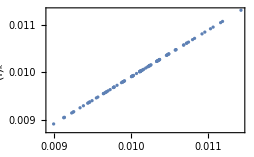

Note that for the higher value of p, the ordering of nodes in terms of their dynamical importance is preserved to a far greater extent by equation (5) than in the case where we have p=0.1. This result is expected and validates our prior analysis, which put forth the idea that for small values of p, percentage differences in total degree across nodes are larger than for networks with high values of p, which translates into large differences in eigenvector centralities across nodes for sufficiently small networks and, as a result, the violation of the condition (v_k u_k)/(v.u)<<1 for all k occurring with higher probability. Now, the command below generates a plot which shows the relationship between the dynamical importance of a node in the two networks generated and (d_k^in d_k^out)^(1/2) for networks in SampleE. Note that, since the ordering of nodes in terms of their dynamical importance is preserved by equation (5) for the sample of networks in SampleE, we can calculate the dynamical importance of each node directly from the equation in question, which is what we do below:

```mathematica
List3={};Do[{u=Eigenvectors[N[SampleE[[i]]]][[1]],v=Eigenvectors[N[Transpose[SampleE[[i]]]]][[1]],T=Table[{(Total[SampleE[[i]]][[k]]Total[Transpose[SampleE[[i]]]][[k]])^(1/2),Re[(u[[k]]v[[k]])/(u.v)]},{k,1,100}],AppendTo[List3,T]},{i,1,Length[SampleE]}];L3=ListPlot[List3,PlotRange->{{0,100},{0,0.065}}, PlotStyle->Blue,Frame->True,FrameLabel->{"(d_k^ind_k^out)^(1/2)","I_k"}];
```

Meanwhile, the list SampleF below contains 500 adjacency matrices corresponding to networks of the the type A2 with the parameters p and γ set to 0.9 and 2 respectively:

```mathematica
SampleF={};Do[AppendTo[SampleF,Subscript[A, 2][0.9,2]],500]
```

Note that the networks comprising SampleF will generally be highly assortative as a result of large p and γ. Just to confirm this numerically, we compute the assortativity of the first network in SampleF:

```mathematica
Assortativity[SampleF[[1]]]//N
```

0.484035

Now, the command below generates a matrix M1, where entry (i,j) of the matrix in question yields the dynamical importance of node j of the network corresponding to the adjacency matrix i in SampleF:

```mathematica
ΔEvnF={};Do[{λ=Eigenvalues[N[SampleF[[i]]]][[1]],f[SampleF[[i]],λ]},{i,1,Length[SampleF]}];M3=ArrayReshape[Re[ΔEvnF],{Length[SampleF],100}];
```

The figure below now demonstrates the accuracy with which the dynamical importances of the nodes are represented by equation (5) from the paper by Restrepo, Ott and Hunt for the first network (chosen arbitrarily) in SampleF:

```mathematica
ListPlot[Table[{-M3[[1,i]],Re[(Eigenvectors[N[SampleF[[1]]]][[1]][[i]]Eigenvectors[N[Transpose[SampleF[[1]]]]][[1]][[i]])/(Eigenvectors[N[SampleF[[1]]]][[1]].Eigenvectors[N[Transpose[SampleF[[1]]]]][[1]])]},{i,1,100}],PlotRange->Full,Frame->True,FrameLabel->{"I_k","(Î)_k"}]
```

Figure 10:

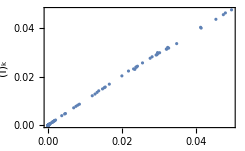

Now, note that the ordering of the nodes in terms of dynamical importance is preserved with greater accuracy by equation (5) for the class of networks A2 by increasing the parameters p and γ from 0.1 and 0.75 to 0.9 and 2 respectively. This is a result of the fact that the effect of increasing the number of links in the network by increasing the value of p (which will help preserve the ordering of the nodes) outweighs the increase in assortativity that results from the increase in the values of p and γ. Note however that the ordering of the nodes is still not fully preserved in this case unlike for the Erdos-Rényi networks generated by setting p=0.9. This is a result of the fact that a network of type A2 generated with parameters p=0.9 and γ=2 is more assortative and has fewer connections than the Erdos-Rényi network in question. The command below now generates a plot which shows the relationship between the dynamical importance of a node and (d_k^in d_k^out)^(1/2) for networks in SampleF. Note that, since the ordering of nodes in terms of their dynamical importance is not preserved by equation (5) for the sample of networks in SampleF, we calculate the dynamical importance of each node from its definition below:

```mathematica
List4={};Do[{T=Table[{(Total[SampleF[[i]]][[k]]Total[Transpose[SampleF[[i]]]][[k]])^(1/2),-M3[[i,k]]},{k,1,100}],AppendTo[List4,T]},{i,1,Length[SampleF]}];L4=ListPlot[List4,PlotRange->{{0,100},{0,0.065}}, PlotStyle->Red,Frame->True,FrameLabel->{"(d_k^ind_k^out)^(1/2)","I_k"}];
```

Finally, the list SampleF below contains 500 adjacency matrices corresponding to networks of the the type A2 with the parameters p and γ set to 0.9 and -10 respectively:

```mathematica
SampleG={};Do[AppendTo[SampleG,Subscript[A, 2][0.9,-10]],500]
```

Note that the networks comprising SampleG will generally be disassortative as a result of large p and very negative γ. The following command now generates an adjacency matrix for the network of the type A2 with parameters p and γ set to 0.9 and -10 respectively. It then creates a list ΔEvnG whose k-th element yields the dynamical importance of node k with respect to the network in question:

```mathematica
C2=Subscript[A, 2][0.9,-10];Subscript[α, 3]=Eigenvalues[N[A4]][[1]];ΔEvnG={};f[A4,Subscript[α, 3]]
```

The plot below shows how accurately the dynamical importances of the nodes in the network C2 are represented by equation (5) from the paper by Restrepo, Ott and Hunt (2006):

```mathematica
ListPlot[Table[{-ΔEvnG[[i]],(Eigenvectors[N[A4]][[1]][[i]]Eigenvectors[N[Transpose[A4]]][[1]][[i]])/(Eigenvectors[N[A4]][[1]].Eigenvectors[N[Transpose[A4]]][[1]])},{i,1,100}],PlotRange->Full,Frame->True,FrameLabel->{"I_k","(Î)_k"}]
```

Figure 11:

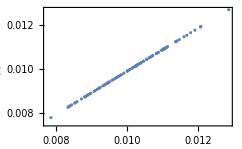

Now, note that for the disassortative networks in SampleG, the ordering of nodes in terms of dynamical importance is preserved even more by equation (5) than for the Erdos-Rényi networks with the same value of p. This is due to the fact that for nodes of higher degree in these networks, which one might expect to have a higher eigenvector centrality, are connected to nodes of lower degree, which ensures that the eigenvector centralities of these nodes will not be too large. Meanwhile, nodes which tend to be connected to nodes of higher degree are themselves of lower degree, which will also moderate the eigenvector centralities of such nodes. Thus, the disassortative property of the network ensures that the eigenvector centralities of all nodes in the network are very similar, which means that the condition (v_k u_k)/(v.u)<<1 holds for all k. The command below now generates a plot which shows the relationship between the dynamical importance of a node and (d_k^in d_k^out)^(1/2) for the networks in SampleG. Note that, since the ordering of nodes in terms of their dynamical importance is preserved by equation (5) for the networks in SampleG, we can calculate the dynamical importance of each node directly from the equation in question, which is what we do below:

```mathematica
List5={};Do[{u=Eigenvectors[N[SampleG[[i]]]][[1]],v=Eigenvectors[N[Transpose[SampleG[[i]]]]][[1]],T=Table[{(Total[SampleG[[i]]][[k]]Total[Transpose[SampleG[[i]]]][[k]])^(1/2),Re[(u[[k]]v[[k]])/(u.v)]},{k,1,100}],AppendTo[List5,T]},{i,1,Length[SampleG]}];L5=ListPlot[List5,PlotRange->{{0,100},{0,0.065}}, PlotStyle->Green,Frame->True,FrameLabel->{"(d_k^ind_k^out)^(1/2)","I_k"}];
```

The plot below now establishes the relationship between the dynamical importance of a node and (d_k^in d_k^out)^(1/2) for networks in the SampleG (which corresponds to the green plot below), SampleF (which corresponds to the red plot below) and SampleE (which corresponds to the blue plot below):

```mathematica
Show[L3,L4,L5]
```

Figure 12:

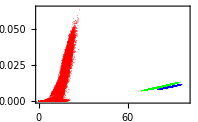

Note that for the assortative networks in SampleF generated above, we now observe an obvious exponential relationship between the variable (d_k^in d_k^out)^(1/2) and the dynamical importance of the node k, which was not apparent in the first plot of this sub-question. This exponential relationship is more prominent in the plot above due to the fact that the assortativity of the networks is greater in SampleF than in SampleD , due to the fact that the parameters p and γ are higher in the former. Meanwhile, for the disassortative networks in SampleG, we observe very little variability in the dynamical importance of nodes as we vary (d_k^in d_k^out)^(1/2), which as referenced above, is due to the fact that nodes with high degree will be connected to nodes with low degree and vice versa, which balances the dynamical importance of nodes in the network and we tend to a situation in which the said dynamical importance is independent of the degree of the nodes. Note that nodes in the disassortative network have a higher degree than the nodes in the assortative network as we had anticipated in a previous sub-question. Finally, note the high variability in (d_k^in d_k^out)^(1/2) for a given value of I_k for the assortative network above, which is a result of the relatively low number of links in the networks comprising SampleF. As a final observation, note that when we retrieve the node with highest dynamical importance in the disassortative network C2, we see that its corresponding point in the plane has horizontal coordinate close to 5, while the node with lowest dynamical important in C2 is associated with a point in the plane which has a very extreme horizontal coordinate, just as we would expect:

```mathematica
List[Position[-ΔEvnG,Max[-ΔEvnG]],Position[-ΔEvnG,Min[-ΔEvnG]]]
```

{{{66}},{{12}}}

```mathematica
List[Nodes[[66]],Nodes[[12]]]
```

{{4.28201,4.41103},{9.12832,0.867786}}

Note that for an assortative network with positive p and γ, these results would be reversed.

### Regular Networks & Network Evolution

I next move from randomly generated networks to a regular two-dimensional square lattice containing 400 nodes arranged in a 20 × 20 structure.

## Square Lattice Construction

I construct the square lattice programmatically as an adjacency matrix and verify its bipartite structure by reordering the matrix into the corresponding block form.

In order to construct an n×n square lattice, we introduce the double index (i,j), where the two indices specified run from 1 to n and each index represents a direction in two dimensional space, in order to label the nodes of the network in question. Hence, we use the basis vectors (ê)_(i,j) to construct said network, which we generate using the command below:

```mathematica
Ev[n_,i_,j_]:=Flatten[Table[If[r==i && s==j,1,0],{r,1,n},{s,1,n}]]
```

The command below now connects the node with label (i,j) to all of its neighbours on a two dimensional grid in order to produce an m×m square lattice. To see how this works, let us take the case of a node labelled by (m,1) for example. This node is on the corner of the two-dimensional m×m grid in question, and as a result will only give rise to two outgoing links to the nodes with labels (m-1,1) and (m,2). The command below ensures that corner links such as these and links on the edge of the lattice which have three connections are of no concern and are represented appropriately since Ev[m,i,j] will return a vector of m zeros for i and j not on the interval [0,m]. Specifically, the expression which represents the outgoing links of the node labelled (m,1) in the command below given by 

TensorProduct[Ev[m,m,1],Ev[m,m+1,1]]+TensorProduct[Ev[m,m,1],Ev[m,m-1,1]]+TensorProduct[Ev[m,m,1],Ev[m,m,2]]+TensorProduct[Ev[m,m,1],Ev[m,m,0]]

which will simplify to TensorProduct[Ev[m,m,1],Ev[m,m-1,1]]+TensorProduct[Ev[m,m,1],Ev[m,m,2]]. The exact same reasoning can be applied to verify that the nodes on the edge of the lattice are properly represented and as a result the command below generates the desired network. Note also that the network produced by the command below is symmetric.

```mathematica
Subscript[B, 1][m_]:=∑_(j=1)^m ∑_(k=1)^m (TensorProduct[Ev[m,j,k],Ev[m,j,k-1]]+TensorProduct[Ev[m,j,k],Ev[m,j,k+1]]+TensorProduct[Ev[m,j,k],Ev[m,j-1,k]]+TensorProduct[Ev[m,j,k],Ev[m,j+1,k]])
```

The command below now generates a 20×20 lattice with 400 nodes:

```mathematica
B1=Subscript[B, 1][20];
```

We now show that the network in question is bipartite. Α graph G is bipartite if its nodes can be divided into 2 disjoint sets, U and V, such that every link connects a node in U to one in V. For an undirected network, this is equivalent to saying that the adjacency matrix A of a bipartite network gives rise to a permutation P such that A=P(0 | X
Y | 0)P^T, where Y=X^T and each row and column of the matrix X has at least one non-zero entry. We now construct such a permutation P for the adjacency matrix B1. Firstly, we define the set of basis vectors (ê)_i:

```mathematica
Eva[n_,i_]:=Flatten[Table[If[r==i ,1,0],{r,1,n}]]
```

Now, the first of the two disjoint sets that make up the bipartite square lattice, which we call U without loss of generality, consists of all nodes which have label (i,j) such that the sum of i and j is even, while the second disjoint set V consists of all nodes which have label (i,j) such that the sum of i and j is odd. Graphically, this means that we can capture all of the points in U by starting from any corner of the lattice and drawing a line through every second diagonal, where the two corner nodes captured by this process are also contained in U. This will yield 200 nodes which make up the set U, while the remaining 200 nodes will comprise V. Now, we use the functions U and V below to generate a permutation P=U+V such that the matrix P.B1.P^T will have its first 200 rows and columns corresponding to the elements of U, with the last 200 rows and columns corresponding to elements of V. Specifically, the first row and column of the matrix in question will correspond to the node with label (1,1) while the next three will correspond to the nodes with labels (3,1),(2,2) and (1,3) respectively and so on. Meanwhile, the 201st and 202nd row and column of the matrix will correspond to the nodes with labels (2,1) and (1,2) while the next four rows and columns will correspond to the nodes with labels (4,1),(3,2),(2,3) and  (1,4) respectively and so on.

```mathematica
U=∑_(n=1)^10 ∑_(i=1)^(2n-1) TensorProduct[Eva[400,(n-1)^2+i],Ev[20,2n-i,i]]+∑_(n=1)^10 ∑_(i=1)^(2n-1) TensorProduct[Eva[400,201-(n-1)^2-i],Ev[20,21-(2n-i),21-i]];V=∑_(n=1)^10 ∑_(i=0)^(2n-1) TensorProduct[Eva[400,201+n(n-1)+i],Ev[20,2n-i,i+1]]+∑_(n=1)^9 ∑_(i=0)^(2n-1) TensorProduct[Eva[400,400-n(n-1)-i],Ev[20,21-(2n-i),20-i]];
```

Summing U and V yields the desired permutation, which we then apply to B1:

```mathematica
P=U+V;BlockMatrix=P.B1.Transpose[P];
```

We now check whether the block matrices X and Y that we have generated satisfy Y=X^T:

```mathematica
BlockMatrix[[201;;400,1;;200]]==Transpose[BlockMatrix[[1;;200,201;;400]]]
```

True

Thus we see that Y=X^T holds. Now, the first two elements of the list below count the number of non-zero elements of the two block matrices on the diagonal of the matrix P.B1.P^T. Meanwhile, the third element of the list below yields the number of columns of Y which consist only of zeroes (which is equal to the number of rows of X that consist only of zeroes). Meanwhile, the fourth element of the list below yields the number of columns of X which consist only of zeroes. Now, we have constructed the permutation correctly if and only if all four elements of the list below are zero:

```mathematica
List[Count[Flatten[BlockMatrix[[1;;200,1;;200]]],x_/;x≠0],Count[Flatten[BlockMatrix[[201;;400,201;;400]]],x_/;x≠0],Count[Total[BlockMatrix[[1;;200,201;;400]]],0],Count[Total[BlockMatrix[[201;;400,1;;200]]],0]]
```

{0,0,0,0}

Thus, we have constructed the permutation correctly and shown that the 20×20 square lattice is bipartite. Note that this implies that any two step path must go from a node in one set to a node in same set, which is why we get following figure when we plot the network corresponding to the adjacency matrix B1^2:

```mathematica
GraphPlot3D[MatrixPower[B1,2]]
```

Figure 13:

-Graphics3D-

## Dynamical Importance in the Square Lattice

I calculate the dynamical importance of the nodes in the square lattice and examine how a node’s position within the regular network affects its importance.

In order to speed up the required computation, we use the property that the square lattice generated is symmetric and produce a list ΔEvn3 which contains only the dynamical importances of the first 200 nodes in the network by adjusting the function f. We then reverse this list and append it to ΔEvn3, which will yield a list containing the dynamical importances of all 400 nodes in the network.

```mathematica
Subscript[λ, 3]=Eigenvalues[B1][[1]];ΔEvn3={};f[B1,Subscript[λ, 3]]
```

The plot below now yields the dynamical importances of all nodes in the network, where the data point k corresponds to the dynamical importance of the node (Ceiling[k/100],If[k/20∈Integers,20,k-20 Floor[k/20]]) of the lattice:

```mathematica
ListPlot[-Join[ΔEvn3,Reverse[ΔEvn3]],Frame->True,FrameLabel->{"k","I_k"}]
```

Figure 14:

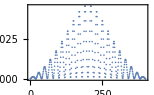

The plot above shows that, for a given row in the square lattice, the more central a node is with respect to its position in that particular row, the higher is its dynamical importance. Similarly, for a given column in the square lattice, the more central a node is with respect to its position in that particular column, the higher is its dynamical importance. As a result, the four most central nodes in the lattice have the highest dynamical importance, while the nodes on the corners of the lattice have the lowest dynamical importance.

## Network Evolution Simulation

I implement an iterative network-evolution algorithm. At each time step, a node is selected at random and its existing connections are removed. It is then reconnected symmetrically to four nodes, with the probability of selecting a target node weighted by its degree. Each resulting adjacency matrix is stored so that the evolution of the network can be analysed over time.

We will evolve the network so that the probability that a node k in the network is selected for reconnection with the randomly selected node whose connections have been removed at any time step is given by d^k/(∑_(k=1)^n d^k), where d^k is the degree of node k. Now, the For command below first takes a network consisting of n nodes A, which it labels N1, and appends it to the empty list NetworkEvolution. It then generates a random integer Q on the interval [1,n] and removes all of the connections of the node with label Q from the network, which results in a new network labelled N2. It then calculates a list DegList, where each node’s label is repeated as many times as the in-degree of that node (note due to symmetry that d^k/(∑_(k=1)^n d^k)=(2 d_in^k)/(2∑_(k=1)^n d_in^k)=d_in^k/(∑_(k=1)^n d_in^k), so that selecting a node k for reconnection with probability equal to its relative frequency in DegList is equivalent to selecting that node for reconnection with probability d^k/(∑_(k=1)^n d^k)). The command then enters a sub-loop where it sets the list DL to be equal to DegList and randomly selects a node k from DL, after which it appends it to an initially empty list called ReconnectList. It then removes all entries k from DL and repeats this process m times. Returning to the first loop, Mathematica now creates a network N3 which symmetrically reconnects the node Q to the m nodes whose labels appear in ReconnectList. The command then appends N3 to the list NetworkEvolution. The process described above is repeated T times, and the end result is the list NetworkEvolution, whose entry i is given by the adjacency matrix corresponding to the evolved network at time t=i. The command F in question is given below:

```mathematica
F[T_,m_,A_]:=For[t=2;{N1=A,NetworkEvolution={N1}},t⩽T,t++,{Q=RandomInteger[{1,Length[N1]}],N2=Transpose[ReplacePart[Transpose[ReplacePart[N1,Q->Table[0,Length[N1]]]],Q->Table[0,Length[N1]]]],HalfDeg=Total[N2],DegList=Flatten[Table[Table[j,{i,1,HalfDeg[[j]]}],{j,1,Length[HalfDeg]}]],For[i=1;{DL=DegList,ReconnectList={}},i⩽m,i++,{RC[i]=RandomChoice[DL],DL=DeleteCases[DL,RC[i]],ReconnectList=Append[ReconnectList,RC[i]]}],N3=N2+Table[If[MemberQ[ReconnectList,i]&&j==Q,1,0],{j,1,Length[N2]},{i,1,Length[N2]}]+Transpose[Table[If[MemberQ[ReconnectList,i]&&j==Q,1,0],{j,1,Length[N2]},{i,1,Length[N2]}]],NetworkEvolution=Append[NetworkEvolution,N3],N1=N3}]
```

In our case, we want to apply the command above to the network described by the adjacency matrix B1, and since we want four reconnections at every iteration of the network’s evolution, we set m=4. Finally, we set the number of time steps for which the network’s evolution occurs to T=1000:

```mathematica
F[1000,4,B1]
```

We call the resultant list NetworkEvolutionS in the case of the square lattice.

## Evolution Analysis

I analyse how the evolution process affects node dynamical importance and local network structure. I compare dynamical importance with the Watts–Strogatz clustering coefficient and also examine its relationship with triangle participation, two-step paths and node degree as the network evolves.

The command p[A] below computes the third power of a given matrix A, the diagonal element k of which yields the number of triangles that the node k is a part of given that A is an unweighted adjacency matrix:

```mathematica
y[A_,n_]:=MatrixPower[A,n];p[A_]:=y[A,3]
```

The command below now generates the matrix A.Q.A (where Q has been defined in part A), the diagonal element k of which yields the number of two step paths running through the node k given that A is an unweighted adjacency matrix:

```mathematica
TwoStep[A_]:=A .Q[Length[A]].A
```

Now, T_1 and TS_1 below yield matrices for which the elements (i,j) yield the number of triangles that the node j is a member of and the number of two-step links going through node j respectively for the network corresponding to the adjacency matrix i of the list NetworkEvolutionS. Meanwhile, the command which yields WS1 below generates a matrix of which element (i,j) yields the Watts-Strogatz coefficient corresponding to node j for the network represented by the adjacency matrix i of NetworkEvolutionS. Finally, WS_1 replaces the readings for nodes with an indeterminate Watts-Strogatz coefficient (i.e. nodes with zero two step paths passing through them) with zero:

```mathematica
Subscript[T, 1]=Map[Diagonal,Map[p,NetworkEvolutionS]];Subscript[TS, 1]=Map[Diagonal,Map[TwoStep,NetworkEvolutionS]];WS1=Subscript[T, 1]/Subscript[TS, 1];Subscript[WS, 1]=ReplacePart[WS1,Position[WS1,Indeterminate]->0];
```

The command below generates a matrix MS, where entry (i,j) of the matrix in question yields the dynamical importance of node j of the network corresponding to the adjacency matrix i in NetworkEvolutionS:

```mathematica
ΔEvnS={};Do[{λ=Eigenvalues[N[NetworkEvolutionS[[i]]]][[1]],f[NetworkEvolutionS[[i]],λ]},{i,1,Length[NetworkEvolutionS]}];MS=ArrayReshape[Re[ΔEvnS],{Length[NetworkEvolutionS],400}];
```

The following set of commands now generates four lists, each of which has element i that yields the correlation of the dynamical importance of a node with some variable for the i-th network in the list NetworkEvolutionS. For the lists CS1,CS2,CS3 and CS4, these variables are the Watts-Strogatz coefficient, the number of triangles that a node belongs to, the number of two step paths running through a node and the degree of a node respectively:

```mathematica
CS1={};Do[{c=If[Total[Subscript[WS, 1][[i]]]==0,Nothing,Correlation[Subscript[WS, 1][[i]],-MS[[i]]]],AppendTo[CS1,c]},{i,1,1000}];CS2={};Do[{c=If[Total[Subscript[T, 1][[i]]]==0,Nothing,Correlation[Subscript[T, 1][[i]],-MS[[i]]]],AppendTo[CS2,c]},{i,1,1000}];CS3={};Do[{c=Correlation[Subscript[TS, 1][[i]],-MS[[i]]],AppendTo[CS3,c]},{i,1,1000}];CS4={};Do[{c=Correlation[Map[Total,NetworkEvolutionS][[i]],-MS[[i]]],AppendTo[CS4,c]},{i,1,1000}]
```

The list below now yields the mean value of each of the four lists generated above:

```mathematica
List[Mean[CS1],Mean[CS2],Mean[CS3],Mean[CS4]]
```

{0.133776,0.403085,0.751628,0.673936}

The following figure now yields a list plot of each of the four lists that we have produced:

```mathematica
GraphicsGrid[{{ListPlot[CS1,Frame->True,FrameLabel->{"t","ρ_(WS, SubscriptBox[I, k])"}],ListPlot[CS2,Frame->True,FrameLabel->{"t","ρ_(Tr, SubscriptBox[I, k])"}],ListPlot[CS3,Frame->True,FrameLabel->{"t","ρ_(TS, SubscriptBox[I, k])"}],ListPlot[CS4,Frame->True,FrameLabel->{"t","ρ_(d, SubscriptBox[I, k])"}]}}]
```

Figure 15:

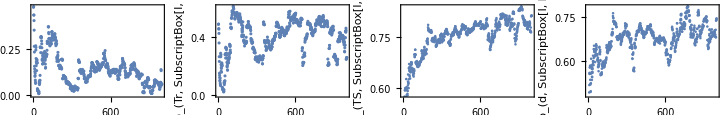

Meanwhile, the assortativity of the evolving square lattice over time is depicted by the list plot below:

```mathematica
ListPlot[Map[Assortativity,NetworkEvolutionS],Frame->True,FrameLabel->{"t","Assortativity"}]
```

Figure 16:

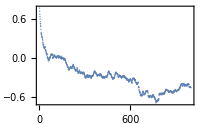

Note that at the start of the square lattice’s evolution we have an assortative network, since peripheral nodes of low degree are highly connected while interior nodes of high degree are highly connected. As the network evolves, nodes which were initially internal to the lattice become highly connected and clustered due to their high starting degree, which further increases the probability that they will form additional connections with reconnecting nodes of far lower degree, which reduces the assortativity of the network until the coefficient levels off at a value of roughly -0.5, while nodes that were peripheral to the network initially lack connectedness as a result of the evolution. Note that the fall in the assortativity of the network as it evolves actually coincides with an increase in the correlation between the degree of the node and their dynamical importance, which is contrary to our findings in Part A. This is likely a result of the fact that the increase in the discrepancies of the degrees of highly connected and relatively unconnected nodes outweighs the reduction in the assortativity of the network as time passes. Note also the trivial result that the number of two step links passing through a node is highly correlated with the dynamical importance of the node in question. Furthermore, due to the high degree of clustering amongst nodes that were internal to the initial square lattice as the network evolves, we also observe a not insignificant correlation between the dynamical importance of a node and the number of triangles that said node is a member of, which results in a statistically significant correlation between a node’s dynamical importance and its Watts-Strogatz coefficient, which as we shall see is not the case when evolving a torus according to the same procedure.

## Toroidal Lattice Comparison

Finally, I repeat the evolution analysis using a toroidal lattice. Connecting opposite boundaries removes the edge effects present in the square lattice and gives every node the same initial degree, allowing me to examine how the network’s initial topology affects its subsequent evolution.

We generate a torus consisting of m^2 nodes by taking the m×m square lattice that we generated above and connecting its opposite edges, which results in a network in which every node has exactly four symmetric links. The command below does this by taking the node with label (m,j) and connecting it to the node with label (1,j)  for all 1⩽j⩽m while also taking the node with label (i,m) and connecting it to the node with label (i,1) for all 1⩽i⩽m. It does this by taking the command used to generate the m×m square lattice produced above and replacing the components x and y in each expression Ev[m,x,y] that is present in the sum that it comprises with Mod[x,m,1] and Mod[y,m,1] respectively. The command Mod[t,m,1] yields a result w such that 1⩽w<m and w mod m=t mod m, meaning that it will return a value of t for 1⩽t⩽m, a value of m for t=0 and a value of 1 for t=m+1. Thus, using the command below, we ensure that all connections of the square lattice exist in the case of the torus, but now for example the node (m,m) which occupies two edges will be connected to the nodes with labels (1,m) and (m,1), the first of which, for demonstration, is represented in the command B_2[m] by the expression: 

TensorProduct[Ev[m,Mod[m,m,1],Mod[m,m,1]],Ev[m,Mod[m+1,m,1],Mod[m,m,1]]] =TensorProduct[Ev[m,m,m],Ev[m,1,m]]

The command in question is given by:

```mathematica
Subscript[B, 2][m_]:=∑_(j=1)^m ∑_(k=1)^m (TensorProduct[Ev[m,Mod[j,m,1],Mod[k,m,1]],Ev[m,Mod[j-1,m,1],Mod[k,m,1]]]+TensorProduct[Ev[m,Mod[j,m,1],Mod[k,m,1]],Ev[m,Mod[j+1,m,1],Mod[k,m,1]]]+TensorProduct[Ev[m,Mod[j,m,1],Mod[k,m,1]],Ev[m,Mod[j,m,1],Mod[k-1,m,1]]]+TensorProduct[Ev[m,Mod[j,m,1],Mod[k,m,1]],Ev[m,Mod[j,m,1],Mod[k+1,m,1]]])
```

The command below now generates a torus with 400 nodes:

```mathematica
B2=Subscript[B, 2][20];
```

We now apply the command F to the torus generated above, again running the evolution for T=1000 time steps and setting the number of reconnections at each iteration to m=4:

```mathematica
F[1000,4,B2]
```

We call the resultant list NetworkEvolutionT in this case. Now, just as we did in the square lattice case, we calculate the Watts-Strogatz coefficient for each node in each iteration of the Torus’ evolution below:

```mathematica
Subscript[T, 2]=Map[Diagonal,Map[p,NetworkEvolutionT]];Subscript[TS, 2]=Map[Diagonal,Map[TwoStep,NetworkEvolutionT]];WS2=Subscript[T, 2]/Subscript[TS, 2];Subscript[WS, 2]=ReplacePart[WS2,Position[WS2,Indeterminate]->0];
```

The command below generates a matrix MT, where entry (i,j) of the matrix in question yields the dynamical importance of node j of the network corresponding to the adjacency matrix i in NetworkEvolutionT:

```mathematica
ΔEvnT={};Do[{λ=Eigenvalues[N[NetworkEvolutionT[[i]]]][[1]],f[NetworkEvolutionT[[i]],λ]},{i,1,Length[NetworkEvolutionT]}];MT=ArrayReshape[Re[ΔEvnT],{Length[NetworkEvolutionT],400}];
```

The following set of commands now generates four lists, each of which has element i that yields the correlation of the dynamical importance of a node with some variable for the i-th network in the list NetworkEvolutionT. For the lists CT1,CT2,CT3 and CT4, these variables are the Watts-Strogatz coefficient, the number of triangles that a node belongs to, the number of two step paths running through a node and the degree of a node respectively:

```mathematica
CT1={};Do[{c=If[Total[Subscript[WS, 2][[i]]]==0,Nothing,Correlation[Subscript[WS, 2][[i]],-MT[[i]]]],AppendTo[CT1,c]},{i,1,1000}];CT2={};Do[{c=If[Total[Subscript[T, 2][[i]]]==0,Nothing,Correlation[Subscript[T, 2][[i]],-MT[[i]]]],AppendTo[CT2,c]},{i,1,1000}];CT3={};Do[{c=Correlation[Subscript[TS, 2][[i]],-MT[[i]]],AppendTo[CT3,c]},{i,2,1000}];CT4={};Do[{c=Correlation[Map[Total,NetworkEvolutionT][[i]],-MT[[i]]],AppendTo[CT4,c]},{i,2,1000}]
```

The list below now yields the mean value of each of the four lists generated above:

```mathematica
List[Mean[CT1],Mean[CT2],Mean[CT3],Mean[CT4]]
```

{0.0482206,0.289553,0.74722,0.689986}

The following figure now yields a list plot of each of the four lists that we have produced:

```mathematica
GraphicsGrid[{{ListPlot[CT1,Frame->True,FrameLabel->{"t","ρ_(WS, SubscriptBox[I, k])"}],ListPlot[CT2,Frame->True,FrameLabel->{"t","ρ_(Tr, SubscriptBox[I, k])"}],ListPlot[CT3,Frame->True,FrameLabel->{"t","ρ_(TS, SubscriptBox[I, k])"}],ListPlot[CT4,Frame->True,FrameLabel->{"t","ρ_(d, SubscriptBox[I, k])"}]}}]
```

Figure 17:

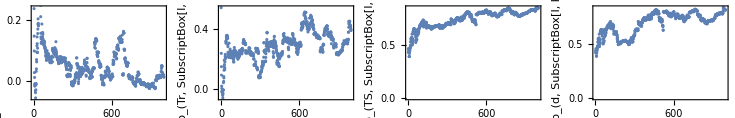

Meanwhile, the assortativity of the evolving torus over time is depicted by the list plot below:

```mathematica
ListPlot[ReplacePart[Map[Assortativity,NetworkEvolutionT],Position[Map[Assortativity,NetworkEvolutionT],Indeterminate->0]],Frame->True,FrameLabel->{"t","Assortativity"}]
```

Figure 18:

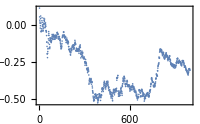

Now, in the case of the torus, some of the results that we observe in the square lattice case still hold. We again see a trend of decreasing assortativity as the network evolves, although the assortativity of the evolved network becomes negative after a much smaller number of iterations in this case, which is a result of the fact that the torus has no variation in its degree across nodes unlike the square lattice, which is an assortative network (note that the jump in assortativity at roughly t=800 is likely a result of a node with very high degree being disconnected from the network). Meanwhile, we again observe that the fall in the assortativity of the network as it evolves actually coincides with an increase in the correlation between the degree of the nodes and their dynamical importance. Furthermore, the correlation between number of two step links passing through the nodes with their dynamical importance is almost identical for the evolving torus as it is for the evolving square lattice. However, note now that the correlation between the number of triangles that a node is a member of and its dynamical importance is far lower than in the square lattice case. This is due to the fact that in the case of the evolution of the torus, each node has the same starting degree, which means that each node has a similar probability of being a site for reconnection as we evolve the network. Meanwhile, in the case of the square lattice, internal nodes have a significantly higher probability of being a site for reconnection than peripheral nodes, meaning that we get a disproportionate number of connections at these nodes and a far higher degree of clustering as we evolve the square lattice than we do as we evolve the torus. This leads to a significantly lower correlation between the Watts-Strogatz coefficient of a node and its dynamical importance for the evolving torus.

# Works Cited:

Restrepo, J. G., Ott, E., & Hunt, B. R. (2006). Characterizing the Dynamical Importance of Network Nodes and Links. Physical Review Letters, 97(9), 1–4. https://doi.org/10.1103/physrevlett.97.094102.